# Učení RBF sítě Demonstrace pokrytí vstupních dat RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí vstupních budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, která obsahují několik dobře oddělených shluků dat.
Vygenerujeme náhodně tyto data.

```mathematica
values=50;
cluster1x =RandomReal[{-10,-8},{values,1}];cluster1y=RandomReal[ {9,12},{values,1}];
cluster2x =RandomReal[{-1,-2},{values,1}];cluster2y=RandomReal[ {-10,-8},{values,1}];
cluster3x =RandomReal[{5,7},{values,1}];cluster3y=RandomReal[ {11,13},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
inDataClass1 = Join[cluster1,cluster2,cluster3];
cluster4x =RandomReal[{-7,-5},{values,1}];cluster4y=RandomReal[ {1,3},{values,1}];
cluster5x =RandomReal[{8,10},{values,1}];cluster5y=RandomReal[ {-4,-2},{values,1}];
cluster6x =RandomReal[{-1,1},{values,1}];cluster6y=RandomReal[ {8,10},{values,1}];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inDataClass2 = Join[cluster4,cluster5,cluster6];
inData= Join[inDataClass1,inDataClass2];
outClass1=ConstantArray[{1,0},{3*values}];outClass2 = ConstantArray[{0,1},{3*values}];
outData= Join[outClass1,outClass2];
```

Takto vypadají naše vynerovaná vstupní data.

```mathematica
inData
```

A takto vypadají data výstupní.

```mathematica
outData
```

Vygenerovaná data si můžeme zobrazit pro lepší představu zobrazit. Každá třída dat má v grafu jinou bavu.

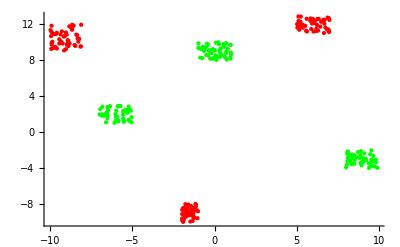

```mathematica
ListPlot[{inDataClass1,inDataClass2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě s jedním RBF neuronem, dvěma vstupy a dvěma výstupy.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,1, OutputNonlinearity->Sigmoid,LinearPart->False,RandomInitialization->True]
```

RBFNet[{{w1, λ, w2}},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 3, 20, 14, 13, 29.0303412}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme chtěli.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-20 at 14:13. The network has 2 inputs and 2 outputs.  It consists of 1 basis function of Exp type. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

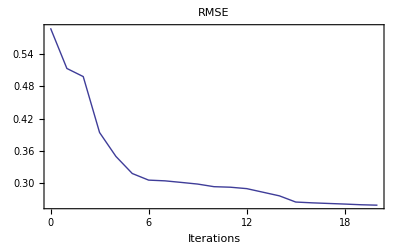

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Podívejme se jak naše síť klasifikuje data.

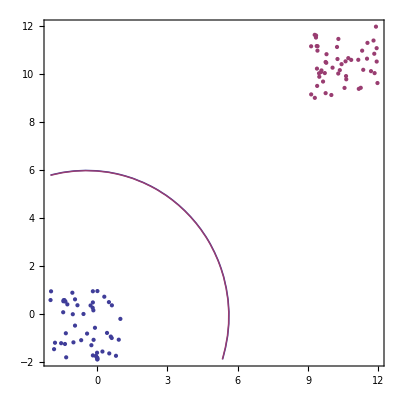

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronů

Nyní se podíváme na “vnitřnosti” neuronové sítě. Naše síť obsahuje jeden RBF neuron, mohlo by být zajímavé zjistit jakou oblast dat tento neuron pokrývá.
Nejprve upravíme síť aby vracela námi požadovaný výstup.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[1],{0}];(*změna matice vah na identickou matici*)
(*net3=NeuronDelete[net3,{0,0}];*)(*odstranění lineární části*)
```

A zobrazíme výstup.

```mathematica
gauss=Plot3D[net3[{x,y}][[1]],{x,-8,16},{y,-8,16},PlotRange->All]
```

-Graphics3D-

Ještě přidáme do grafu vstupní data pro lepší představu o jejich pokrytí.

```mathematica
cluster13d=cluster1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.501};
cluster23d=cluster2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.501};
gaussO=Plot3D[net3[{x,y}][[1]],{x,-8,16},{y,-8,16},PlotRange->All,PlotStyle->Opacity[0.5]];
data3d=ListPointPlot3D[{cluster13d,cluster23d},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
Show[gaussO,data3d]
```

-Graphics3D-